## Routines

```mathematica
(*VFPdata=Import["/Users/hardindp/Dropbox/MinEnergyComputations/minEnergy/Graphics/qhull output/total.txt","Table"];*)
```

```mathematica
VFP[VFPdata_]:=Module[{VFstart,VFend, Vstart, Vend, Fstart, Fend,numPts,numFacets,dim, VertFacets,Verts,Facets,numNN},
numPts=VFPdata[[1,1]];
VFstart=2;VFend=numPts+1;
dim=VFPdata[[VFend+1,1]];
VertFacets= Map[Drop[#,1]+1&,VFPdata[[VFstart;;VFend]]];
numNN= Map[ #[[1]]&,VFPdata[[VFstart;;VFend]]];
Vstart=VFend+3;
 Vend=Vstart+numPts-1;
numFacets=VFPdata[[Vend+1,1]];
Verts=VFPdata[[Vstart;;Vend]];
Fstart=Vend+2;
Fend=Fstart+VFPdata[[Vend+1,1]]-1;
Facets=Map[Drop[#,1]+1&,VFPdata[[Fstart;;Fend]]];
{{dim, numPts,numFacets},numNN,VertFacets,Verts,Facets}];
```

```mathematica
GetVertFacets[VFPfile_]:=VFPfile[[3]]
GetVerts[VFPfile_]:=VFPfile[[4]]
GetFacets[VFPfile_]:=VFPfile[[5]]
GetnumNN[VFPfile_]:=VFPfile[[2]]
NumVerts[VFPfile_]:= Length[VFPfile[[4]]]
```

```mathematica
CircCenter[{u1_,u2_,u3_}]:=Module[{c1,c2,c3,v},
{c1,c2}={-((-1+u1.u2+u1.u3-u2.u3) (-1+u2.u3))/(-3+(u1.u2)^2+2 u1.u3+(u1.u3-u2.u3)^2+2 u2.u3-2 u1.u2 (-1+u1.u3+u2.u3)),((-1+u1.u3) (1-u1.u2+u1.u3-u2.u3))/(-3+(u1.u2)^2+2 u1.u3+(u1.u3-u2.u3)^2+2 u2.u3-2 u1.u2 (-1+u1.u3+u2.u3))};
c3=1-c1-c2;
v={c1,c2,c3}.{u1,u2,u3};
v=v/Sqrt[v.v]]
```

```mathematica
NextFacet[ptIndex_,OtherPtIndex_,Facets_,currFacetIndex_]:= Module[{nextFacet,nextPtIndex},
nextFacet=Complement[Position[Facets,OtherPtIndex][[All,1]],{currFacetIndex}][[1]];
nextPtIndex=Complement[Facets[[nextFacet]],{ptIndex,OtherPtIndex}][[1]];
{nextFacet,nextPtIndex}]
```

```mathematica
VorCell[VFPfile_,ptIndex_]:=Module[{VorVerts,theFacets, theEdge},
theFacets=GetFacets[VFPfile][[GetVertFacets[VFPfile][[ptIndex]]]];
Map[CircCenter,Partition[GetVerts[VFPfile][[Flatten[theFacets]]],3] ]]
```

```mathematica
VorCelltoTris[verts_,pt_]:={EdgeForm[],Switch[Length[verts],5,RGBColor[0,0,1],6,RGBColor[0,1,0],7,RGBColor[1,0,0],_,White],Triangle[Append[Table[{verts[[k]],verts[[k+1]],pt},{k,1,Length[verts]-1}],{verts[[-1]],verts[[1]],pt}]],{Black,Line[Append[verts,verts[[1]]]]}}
```

```mathematica
VorCelltoPolygon[verts_]:={Switch[Length[verts],5,RGBColor[0,0,1],6,RGBColor[0,1,0],7,RGBColor[1,0,0],_,White],Polygon[verts]}
```

```mathematica
VorCelltoPolygon2[verts_]:=Polygon[verts]
```

```mathematica
VorCells[VFPFiles_]:=Table[VorCell[VFPFiles,k],{k,1,VFPFiles[[1,2]]}]
```

```mathematica
VorGraph[VFPFiles_]:=Table[VorCelltoPolygon[VorCell[VFPFiles,k]],{k,1,NumVerts[VFPFiles]}];
```

```mathematica
VorGraph2[VFPFiles_]:=Table[VorCell[VFPFiles,k],{k,1,NumVerts[VFPFiles]}];
```

```mathematica
PlotThisFile[VFPData_]:= Module[{path,VFPFiles},
VFPFiles=VFP[VFPData];
Graphics3D[ {Thickness[.000001],PointSize[.001],VorGraph[VFPFiles],Black,Map[Point,1.003*GetVerts[VFPFiles]]},Boxed->False]
]
```

```mathematica
GetTriangles[VFPfile_,ptIndex_]:=Module[{VorVerts,theFacets, theEdge},
theFacets=GetFacets[VFPfile][[GetVertFacets[VFPfile][[ptIndex]]]];
Partition[GetVerts[VFPfile][[Flatten[theFacets]]],3] ]
```

```mathematica
GetAllTriangle[VFPfile_]:=Union[Flatten[Table[GetTriangles[VFPfile,i],{i,1,VFPfile[[1,2]]}],1]]
```

## Test Conjecture

```mathematica
TestFiles=Import["/Users/ken/Desktop/research/Experiment By Ken/jun13test1600/total10.txt","Table"];
```

```mathematica
PlotThisFile[TestFiles];
```

```mathematica
VFile = VFP[TestFiles];
```

```mathematica
Triangles=GetAllTriangle[VFile];
```

```mathematica
d=3;
```

#### #1 calculate the geodesic radius of a facet on the sphere

```mathematica
t1 = Triangles[[1]]
```

{{-0.997243,-0.073932,0.006367},{-0.997305,-0.023303,-0.069575},{-0.999604,0.020284,0.019525}}

```mathematica
ccenter=CircCenter[t1]
```

{-0.999629,-0.0230176,-0.0145333}

```mathematica
2*Sin[ArcCos[t1[[1]].ccenter]/2]
```

0.0550882

```mathematica
rho=Table[2*Sin[ArcCos[Triangles[[i]][[1]].CircCenter[Triangles[[i]]]]/2],{i,1,Length[Triangles]}];
```

#### #2 plot N^(1/d)*rho

```mathematica
t=VFile[[1,2]]^(1/d);
```

```mathematica
update=rho*t;
```

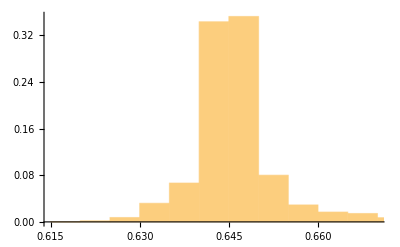

```mathematica
graph1=Histogram[update,Automatic,"Probability"]
```

#### #3 calculate kappa

```mathematica
omega=Table[(2*Pi)^((d+1)/2)/(Gamma[(d+1)/2]),{d,1,10}];
```

```mathematica
kappa=omega[[d-1]]/(d*omega[[d]]);
```

```mathematica
f[x_]:=d/Gamma[d]*(kappa^d)*(x^(d^2-1))*(E^(-kappa*x^d))
```

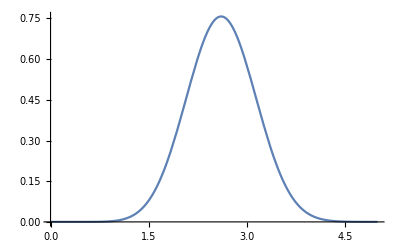

```mathematica
graph2=Plot[f[x],{x,0,5}]
```

#### #4 compare the graph

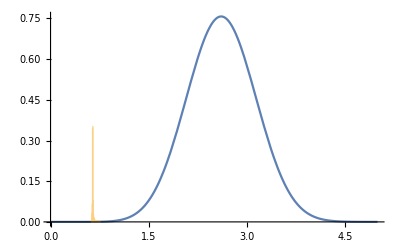

```mathematica
Show[graph2,graph1]
```